```mathematica
Clear[Subscript[R, t],Subscript[R, j],Subscript[C, t],Subscript[C, w],ρ,μ,ω,δ,τ];Clear[Subscript[K, cb],Subscript[K, cd],Subscript[K, Cs],Subscript[K, Lc],b,Subscript[l, c],Subscript[R, c],Subscript[N, s],Subscript[l, s],Subscript[R, s],Subscript[L, 0],Subscript[R, s],Subscript[L, 0],Subscript[L, c],Subscript[C, s],Subscript[C, c],Subscript[ω, 0],Q]
```

Clear::ssym: R_t is not a symbol or a valid string pattern.

Clear::ssym: R_j is not a symbol or a valid string pattern.

Clear::ssym: C_t is not a symbol or a valid string pattern.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

```mathematica
Clear[ω]
```

```mathematica
Clear[d](*In this calculation we are assuming the copper wire's gap τ of the main coil is the same as the diameter of the copper wire. Also by expressing the total length of the main coil "b" as a function of d, now the only parameter we need to play with is d vs Q*);Subscript[D, 0]=15*10^-2(*Subscript[D, 0] is the diameter of the helical shield*);Subscript[d, 0]=5*10^-3(*Subscript[d, 0] is the diameter of the copper wire of the main coil*);Subscript[R, t]=2(*Parameters based on paper "(Helical Resonator - 2014 Amherst College) Constructing an Ultra-High Vacuum Chamber and a Radio Frequency Helical Resonator for Trapping Ions"*);Subscript[R, j]=0.5;Subscript[C, t]=8*10^-12;Subscript[C, w]=0.1*10^-12;ρ=1.678*10^-8;μ=1.2566290*10^-6;ω=2*Pi*20*10^6;
δ=√((2*ρ)/(2*Pi*ω*μ));τ=2*Subscript[d, 0];
Subscript[K, cb]=11.26*10^-12;Subscript[K, cd]=35*d*10^-12;Subscript[K, Cs]=39.37*(0.75/Log[10,Subscript[D, 0]/d])*10^-12;Subscript[K, Lc]=(3.937*d^2)/(4*τ^2)*(1-(d/Subscript[D, 0])^2)*10^-6;b[d_]:=(Subscript[C, w]+Subscript[C, t]+Subscript[K, cd])/(Subscript[K, Cs]+Subscript[K, cb])*(√((Subscript[K, Cs]+Subscript[K, cb])/((Subscript[C, w]+Subscript[C, t]+Subscript[K, cd])^2*Subscript[K, Lc]*ω^2)+1/4)-1/2);Subscript[l, c]=b[d]/τ*√((τ)^2+(Pi*d)^2);Subscript[R, c]=(ρ*Subscript[l, c])/(Subscript[d, 0]*Pi*δ);
Subscript[N, s]=(b[d]*Subscript[l, c])/(4*Pi*(Subscript[D, 0]-d)^2);Subscript[l, s]=Subscript[N, s]*√((Pi*Subscript[D, 0])^2+(b[d]/Subscript[N, s])^2);Subscript[R, s]=(Subscript[N, s]*ρ*Subscript[l, s])/(b[d]*δ);
Subscript[L, 0]=(3.948*b[d]*d^2)/(4*τ^2)*K*10^-6;Subscript[L, c]=b[d]*Subscript[K, Lc];
Subscript[C, s]=39.37*((0.75*b[d])/Log[10,Subscript[D, 0]/d])*10^-12;
Subscript[K, cb]=11.26*10^-12;Subscript[K, cd]=35*d*10^-12;Subscript[C, c]=Subscript[K, cb]*b[d]+Subscript[K, cd];
Subscript[ω, 0]=1/(√((Subscript[C, w]+Subscript[C, t]+Subscript[C, c]+Subscript[C, s])*Subscript[L, c]));Q[d_]:=(ω*Subscript[L, c])/(Subscript[R, j]+Subscript[R, c]+Subscript[R, s]+Subscript[R, t]*(Subscript[C, t]/(Subscript[C, t]+Subscript[C, w]+Subscript[C, s]))^2);FindMaximum[{Q[d],0.00001<=d<=0.099,b[d]/d>=1},{d,0.05}]
```

{288.887,{d→0.0706615}}

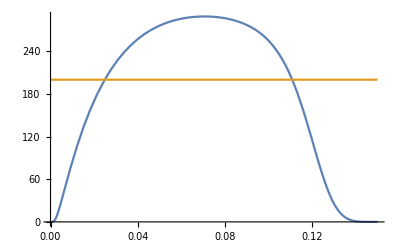

```mathematica
Clear[d];Plot[{Q[d],200},{d,0.00001,0.15}]
```

```mathematica
d=0.0706615217156421;b[d]
```

0.0858386